```mathematica
F[x1_,x2_]=x1^4+x2^4-2 x1^2 -4x1 x2-2 x2^2 ; (* задана функція *)
X={{1.,-1.}}; (*початкове наближення*)
ϵ=10^-3; (*задана точність*)
```

```mathematica
(*значення мінімума, знайдене за допомогою вбудованої функції*)
```

```mathematica
MinF=FindMinimum[F[x1,x2],{{x1,X[[-1,1]]},{x2,X[[-1,2]]}}][[2,1;;2,2]]
```

{1.41421,1.41421}

```mathematica
(*графік тривимірної реалізації*)
Show[Plot3D[F[x,y],{x,-4,4},{y,-4,4}]]
```

-Graphics3D-

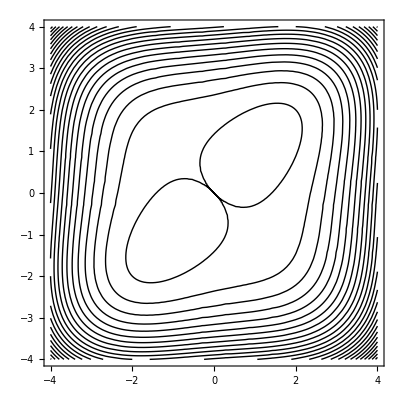

```mathematica
(*двовимірний графік ліній рівня*) 
CP=ContourPlot[F[x,y],{x,-4,4},{y,-4,4},Contours->{Automatic,50},ContourShading->None,AspectRatio->Automatic]
```

```mathematica
(* Метод покоординатного спуску *)
```

```mathematica
t20=AbsoluteTime[]; (*початок відліку часу*)
X2=X;
n=2;
xr=X2[[-1]];
k=1;
res2={};
Xr={x1,x2};
While[Norm[Grad[F[x1,x2],{x1,x2}]/.{x1->X2[[-1,1]],x2->X2[[-1,2]]}]>ϵ,{
If[Length[X2]≥1000,Break[]];
xr=X2[[-1]];
r=1;
While[r≤n,{
If[Abs[D[F[x1,x2],Xr[[r]]]/.{x1->X2[[-1,1]],x2->X2[[-1,2]]}]≤ ϵ,{
r++;
Continue[]; 
},{

xr[[r]]=X2[[-1,r]]-(D[F[x1,x2],Xr[[r]]]/.{x1->X2[[-1,1]],x2->X2[[-1,2]]})/(D[F[x1,x2],{Xr[[r]],2}]/.{x1->X2[[-1,1]],x2->X2[[-1,2]]});
If[r==1,AppendTo[X2,{xr[[r]],X2[[-1,2]]}]];
If[r==2,AppendTo[X2,{X2[[-1,1]],xr[[r]]}]];
AppendTo[res2,{k++,X2[[-1]],F[X2[[-1,1]],X2[[-1,2]]]}];
r++;
}];

}];

If[Norm[Grad[F[x1,x2],{x1,x2}]/.{x1->xr[[1]],x2->xr[[2]]}]>ϵ,{

},{

Break[];
}]
}];
t21=AbsoluteTime[];
Grid[Prepend[res2,{"k","x^*","F(x^*)"}]]
Print["Час роботи методу: ",t2=t21-t20,"\nТочне наближення: ", X2[[-1]],"\nЗначеня функції в отриманому значенні: ", F[X2[[-1,1]],X2[[-1,2]]]]
```

k | x^* | F(x^*)
1 | {0.5,-1.} | 0.5625
2 | {0.5,-0.75} | 0.253906
3 | {2.,-0.75} | 13.1914
4 | {2.,1.68182} | -3.11109
5 | {1.60744,1.68182} | -6.96161
6 | {1.60744,1.48574} | -7.58647
7 | {1.45041,1.48574} | -7.94374
8 | {1.45041,1.42464} | -7.98705
9 | {1.41724,1.42464} | -7.99894
10 | {1.41724,1.4149} | -7.99991
11 | {1.41436,1.4149} | -8.
12 | {1.41436,1.41424} | -8.
13 | {1.41422,1.41424} | -8.

Час роботи методу: 0.014942
Точне наближення: {1.41422,1.41424}
Значеня функції в отриманому значенні: -8.

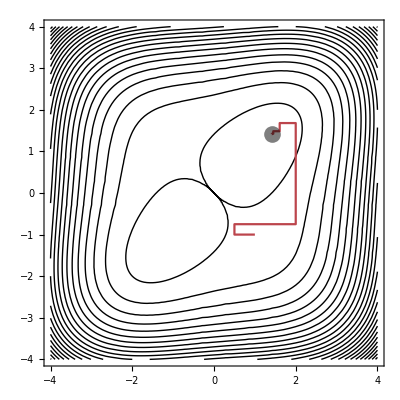

```mathematica
(*траєкторія пошука мінімума функції*)
Show[CP,ListLinePlot[X2,ColorFunction->"Rainbow",PlotRange->All],Graphics[{Opacity[0.5],Black,PointSize[0.03],Point[{MinF[[1]],MinF[[2]]}]}]]
```